```mathematica
ord=7;
P[x_,j_,h_]:=(2-x)x(6-2j-2x)^2-h^2;
Rts=AsymptoticSolve[P[x,j,h*e]==0,x,{e,0,ord+1}];
a=FullSimplify[Rts[[2,1]][[2]],e>0&&h>0&&1<j<3];
c=FullSimplify[Rts[[3,1]][[2]],e>0&&h>0&&1<j<3];
b=FullSimplify[Rts[[4,1]][[2]],e>0&&h>0&&1<j<3];
d=FullSimplify[Rts[[1,1]][[2]],e>0&&h>0&&1<j<3];
```

```mathematica
k2:=((a-b)(c-d))/((a-c)(b-d));
g:=2/Sqrt[(a-c)(b-d)];
β1:=ArcSin[Sqrt[((b-d)(-3+c+j))/((b-c)(-3+d+j))]];
β2:=ArcSin[Sqrt[((a-c)(-2+d))/((a-d)(-2+c))]];
Sinβ2=Sqrt[((a-c)(-2+d))/((a-d)(-2+c))];
Sinβ1=Sqrt[((b-d)(-3+c+j))/((b-c)(-3+d+j))];
c1:=-h*e*g*(1+(j-3)/(2(3-j-d))-1/(2(2-c)));
c2:=-Pi/2*h*e*(j-3)*1/Sqrt[(-3+a+j)(-3+b+j)(-3+c+j)(-3+d+j)];
c3:=-Pi/2*h*e*1/Sqrt[(2-a)(2-b)(2-c)(2-d)];
```

```mathematica
Expk2=FullSimplify[Series[k2,{e,0,ord+1}],1<j<3&&e>0&&h>0&&1<j<3];
Expg=FullSimplify[Series[g,{e,0,ord+1}],1<j<3&&e>0&&h>0&&1<j<3];
Expβ1=FullSimplify[Assuming[e>0&&h>0&&1<j<3,Series[2ArcTan[Sinβ1/(1+Sqrt[1-Sinβ1^2])],{e,0,ord+1}]]];
Expβ2=FullSimplify[Series[2ArcTan[Sinβ2/(1+Sqrt[1-Sinβ2^2])],{e,0,ord+1}],e>0&&h>0&&1<j<3];
Expc1=FullSimplify[Series[c1,{e,0,ord+1}],1<j<3&&e>0&&h>0&&1<j<3];
Expc2=FullSimplify[Series[c2,{e,0,ord+1}],1<j<3&&e>0&&h>0&&1<j<3];
Expc3=FullSimplify[Series[c3,{e,0,ord+1}],1<j<3&&e>0&&h>0&&1<j<3];
Expsincosβ1=FullSimplify[Series[Sin[β1]Cos[β1],{e,0,ord+1}],1<j<3&&e>0&&h>0&&1<j<3];
Expsincosβ2=FullSimplify[Series[Sin[β2]Cos[β2],{e,0,ord+1}],1<j<3&&e>0&&h>0&&1<j<3];
ExpSin2β1=FullSimplify[Series[Sin[β1]^2,{e,0,ord+1}],1<j<3&&e>0&&h>0&&1<j<3];
ExpSin2β2=FullSimplify[Series[Sin[β2]^2,{e,0,ord+1}],1<j<3&&e>0&&h>0&&1<j<3];
```

```mathematica
Λev[ϕ_,k_]:=2/π*(EllipticK[k]*EllipticE[ϕ,1-k ]-(EllipticK[k]-EllipticE[k])*EllipticF[ϕ,1-k]);
```

```mathematica
temp0[kp_]=Normal[Series[EllipticK[1-kp],{kp,0,ord+1}]]//Simplify;
ExpElK[k_]=temp0[1-k];
temp1[kp_]=Normal[Series[EllipticE[1-kp],{kp,0,ord+1}]]// Simplify;
ExpElE[k_]=temp1[1-k];
temp2[ϕ_,kp_]=Normal[Series[Λev[ϕ,1-kp],{kp,0,ord+1}]]//Simplify;
ExpElΛ[ϕ_,k_]=temp2[ϕ,1-k];
```

```mathematica
nolog0[kp_]=Select[Expand[temp0[kp]],FreeQ[#,Log]&];
haslog0[kp_]=temp0[kp]-nolog0[kp]//Expand//FullSimplify;
logterm0[kp_]=Log[kp/16];
logfactor0[kp_]=haslog0[kp]/logterm0[kp]//Factor//Expand;
ExpElkfactorlog[k_]=logfactor0[1-k];
ExpElKlog[k_]=(logfactor0[1-k]*logterm0[1-k]);
ExpElKnolog[k_]=nolog0[1-k];
```

```mathematica
nolog1[kp_]=Select[Expand[temp1[kp]],FreeQ[#,Log]&];
haslog1[kp_]=temp1[kp]-nolog1[kp] // Expand // FullSimplify;
logterm1[kp_]=Log[kp/16];
logfactor1[kp_]=haslog1[kp]/logterm1[kp] // Factor // Expand;
ExpElEfaclog[k_]=logfactor1[1-k] // FullSimplify;
ExpElElog[k_]=(logfactor1[1-k]*logterm1[1-k]);
ExpElEnolog[k_]=nolog1[1-k];
```

```mathematica
nolog2[ϕ_,kp_]=Select[Expand[temp2[ϕ,kp]],FreeQ[#,Log]&];
haslog2[ϕ_,kp_]=temp2[ϕ,kp]-nolog2[ϕ,kp] // Expand // FullSimplify;
logterm2[ϕ_,kp_]=Log[kp/16];
logfactor2[ϕ_,kp_]=haslog2[ϕ,kp]/logterm2[ϕ,kp] // Factor // Expand;
ExpElΛfaclog[ϕ_,k_]=logfactor2[ϕ,1-k];
ExpElΛlog[ϕ_,k_]=(logfactor2[ϕ,1-k]*logterm2[ϕ,1-k]);
ExpElΛnolog[ϕ_,k_]=nolog2[ϕ,1-k];
```

```mathematica
trigfac=Cos[ϕ] Sin[ϕ];
subcos =  Table[ Cos[ϕ]^(2i) -> ( 1 - Sin[ϕ]^2)^i , { i, 1, 2*(ord+1)}];
nolosino= Collect[ (( nolog2[ϕ,kp] - 2 ϕ/π) /trigfac//TrigExpand//Factor) /.subcos//Expand, kp];
lofasino= Collect[ (logfactor2[ϕ,kp]/trigfac//TrigExpand//Factor) /.subcos//Expand, kp];
ExpElΛfaclog2[ϕ_,sincosphi_,sin2phi_, k_]= sincosphi(( lofasino) /. kp -> 1 - k/. {Sin[ϕ]^2 -> sin2phi,Sin[ϕ]^4->sin2phi^2,Sin[ϕ]^6->sin2phi^3,Sin[ϕ]^8->sin2phi^4,Sin[ϕ]^10->sin2phi^5,Sin[ϕ]^12->sin2phi^6,Sin[ϕ]^14->sin2phi^7});
ExpElΛlog2[ϕ_, sincosphi_,sin2phi_, k_]= sincosphi(( lofasino logterm0[kp]) /. kp -> 1 - k/. {Sin[ϕ]^2 -> sin2phi,Sin[ϕ]^4->sin2phi^2,Sin[ϕ]^6->sin2phi^3,Sin[ϕ]^8->sin2phi^4,Sin[ϕ]^10->sin2phi^5,Sin[ϕ]^12->sin2phi^6,Sin[ϕ]^14->sin2phi^7});
ExpElΛnolog2[ϕ_, sincosphi_,sin2phi_,k_]= 2 ϕ/π + sincosphi(nolosino  /. kp -> 1 - k/. {Sin[ϕ]^2 -> sin2phi,Sin[ϕ]^4->sin2phi^2,Sin[ϕ]^6->sin2phi^3,Sin[ϕ]^8->sin2phi^4,Sin[ϕ]^10->sin2phi^5,Sin[ϕ]^12->sin2phi^6,Sin[ϕ]^14->sin2phi^7});
```

```mathematica
Logterm[j_,h_]=Log[2]+Log[Sqrt[h^2]]-3/2*Log[(3-j)(j-1)];
Extrak2[j_,h_]=((1-(Normal[Expk2]/.e->1))/16)/(2*Sqrt[h^2]/((3-j)(j-1))^(3/2));
ExplogExtrak2[j_,h_]=Series[Log[Extrak2[j,h]]/.{h->h*e},{e,0,ord}];
Action1factorlog=FullSimplify[Normal[Series[((Normal[Expc1]/.e->1)*(Normal[ExpElkfactorlog[Expk2]]/.e->1))/.{h->h*e},{e,0,ord}]],e>0&&h>0&&1<j<3];
Action1log=FullSimplify[Action1factorlog*Logterm[j,h*e],1<j<3&&e>0&&h>0] ;
Action1nolog=FullSimplify[Series[Normal[Expc1*(ExpElKnolog[Expk2]+ExpElkfactorlog[Expk2]*ExplogExtrak2[j,h])],{e,0,ord}],1<j<3&&e>0&&h>0];
Action3nolog=FullSimplify[Series[((Normal[Expc2]+Normal[Expc3])/.e->1)/.{h->h*e},{e,0,ord}],1<j<3&&e>0&&h>0];
Action4faclog=FullSimplify[Series[((Normal[-Expc2]/.e->1)*(Normal[ExpElΛfaclog2[Expβ1,Expsincosβ1,ExpSin2β1,Expk2]]/.e->1)+(Normal[-Expc3]/.e->1)*(Normal[ExpElΛfaclog2[Expβ2,Expsincosβ2,ExpSin2β2,Expk2]]/.e->1))/.{h->h*e},{e,0,ord}],e>0&&h>0&&1<j<3];
Action4log=Action4faclog*Logterm[l*e,h*e];
Action4nolog=Module[{term11,term12,term21,term22},
term11=FullSimplify[ExpElΛnolog2[Expβ1,Expsincosβ1,ExpSin2β1,Expk2],1<j<3&&e>0&&h>0];
term12=FullSimplify[ExpElΛfaclog2[Expβ1,Expsincosβ1,ExpSin2β1,Expk2]*ExplogExtrak2[j,h],1<j<3&&e>0&&h>0];
term21=FullSimplify[ExpElΛnolog2[Expβ2,Expsincosβ2,ExpSin2β2,Expk2],1<j<3&&e>0&&h>0];
term22=FullSimplify[ExpElΛfaclog2[Expβ2,Expsincosβ2,ExpSin2β2,Expk2]*ExplogExtrak2[j,h],1<j<3&&e>0&&h>0];
Simplify[Series[Normal[-Expc2*(term11+term12)-Expc3*(term21+term22)],{e,0,ord}],1<j<3&&e>0&&h>0]
];
```

```mathematica
Actionnolog=FullSimplify[(Action1nolog+Action3nolog+Action4nolog),1<j<3&&e>0&&h>0];
```

```mathematica
Coefficient[Actionnolog,e,0]
```

-1/2 (-3+j) π

```mathematica
FullSimplify[Coefficient[Actionnolog,e,1],1<j<3&&h>0&&e>0]
```

-(h (1+Log[16]))/(2 √(-((-3+j) (-1+j))))

```mathematica
Coefficient[Actionnolog,e,2]
```

0

```mathematica
FullSimplify[Coefficient[Actionnolog,e,3],1<j<3&&h>0&&e>0]
```

-(h^3 (-74-(-4+j) j (22+(-4+j) j-24 Log[2])+102 Log[2]))/(48 (-((-3+j) (-1+j)))^(7/2))

```mathematica
FullSimplify[Coefficient[Actionnolog,e,4],1<j<3&&h>0&&e>0]
```

0

```mathematica
FullSimplify[Coefficient[Actionnolog,e,5],1<j<3&&h>0&&e>0]
```

(h^5 (210267-269640 Log[2]-16 (-4+j) j ((-4+j) j (-771+2 (-4+j) j (2+(-4+j) j)+840 Log[2])+1260 (-5+Log[64]))))/(20480 (-((-3+j) (-1+j)))^(13/2))

```mathematica
Actionfaclog=Collect[FullSimplify[Normal[Action1factorlog+Action4faclog],e>0&&h>0&&1<j<3] ,e];
O1=FullSimplify[Coefficient[Actionfaclog,e,1] ,1<j<3&&e>0&&h!=0]
O2=FullSimplify[Coefficient[Actionfaclog,e,2] ,1<j<3&&e>0&&h!=0]
O3=FullSimplify[Coefficient[Actionfaclog,e,3] ,1<j<3&&e>0&&h>0]
O4=FullSimplify[Coefficient[Actionfaclog,e,4] ,1<j<3&&e>0&&h!=0]
O5=FullSimplify[Coefficient[Actionfaclog,e,5],1<j<3&&e>0&&h!=0]
```

h/(2 √(-((-3+j) (-1+j))))

0

(h^3 (17+4 (-4+j) j))/(32 (-((-3+j) (-1+j)))^(7/2))

0

(21 h^5 (321+16 (-4+j) j (9+(-4+j) j)))/(2048 (-((-3+j) (-1+j)))^(13/2))

```mathematica
J2ser=-2*(Actionfaclog)
Normal[J2ser]/.e->1;
Series[%,{h,0,ord}];
InverseSeries[%,h2];
BNF=FullSimplify[Series[Normal[%]/.{h2->h2*e},{e,0,ord}] ,1<j<3&&e>0&&h!=0]
```

-2 (-(e h (-3+j)^9 (-1+j)^9)/(2 (-((-3+j) (-1+j)))^(19/2))+(e^3 h^3 (-3+j)^6 (-1+j)^6 (17+4 (-4+j) j))/(32 (-((-3+j) (-1+j)))^(19/2))-(21 e^5 h^5 (-3+j)^3 (-1+j)^3 (321+16 (-4+j) j (9+(-4+j) j)))/(2048 (-((-3+j) (-1+j)))^(19/2))+(165 e^7 h^7 (6161+4 (-4+j) j (1017+2 (-4+j) j (111+8 (-4+j) j))))/(32768 (-((-3+j) (-1+j)))^(19/2)))

-h2 √(-((-3+j) (-1+j))) e+(h2^3 (17+4 (-4+j) j) e^3)/(16 (-((-3+j) (-1+j)))^(3/2))+(3 h2^5 (1091+16 (-4+j) j (29+3 (-4+j) j)) e^5)/(1024 (-((-3+j) (-1+j)))^(7/2))+(3 h2^7 (111871+4 (-4+j) j (17559+2 (-4+j) j (1801+120 (-4+j) j))) e^7)/(16384 (-((-3+j) (-1+j)))^(11/2))+O[e]^8

```mathematica
Action=Simplify[(Normal[Actionnolog]/.e->1)+((2Normal[Actionfaclog]*Logterm[j,h])/.e->1),h>0];
```

```mathematica
ActionB=(Action/.h->Normal[BNF])/.e->1;
```

```mathematica
ExpAction=Simplify[Collect[Normal[Series[ActionB/.{h2->h2*e} ,{e,0,ord}]] ,e],e>0&&h2<0&&1<j<3];
```

```mathematica
FullSimplify[Coefficient[ExpAction,e,0],1<j<3&&h2>0&&e>0]
```

-1/2 (-3+j) π

```mathematica
FullSimplify[(Normal[Coefficient [ExpAction,e,1]]/.e->1),1<j<3&&h2<0&&e>0]
```

1/2 h2 (1+Log[4]+Log[1/h2^2]+2 Log[-((-3+j) (-1+j))])

```mathematica
FullSimplify[Coefficient[Normal[ExpAction/.e->1],h2^2],1<j<3&&h2<0&&e>0]
```

0

```mathematica
FullSimplify[Coefficient[Normal[ExpAction/.e->1],h2^3],1<j<3&&h2>0&&e>0]
```

-(97+2 (-4+j) j (16+(-4+j) j))/(96 (3-4 j+j^2)^2)

```mathematica
FullSimplify[Coefficient[ExpAction/.e->1,h2^4]/.e->1  ,1<j<3&&h2<0]
```

0

```mathematica
FullSimplify[Coefficient[ExpAction/.e->1,h2^5]/.e->1  ,1<j<3&&h2<0]
```

(-65337+32 (-4+j) j (-870+(-4+j) j (-58+(-4+j) j (12+(-4+j) j))))/(20480 (3-4 j+j^2)^4)

```mathematica
Collect[FullSimplify[D[Normal[ExpAction]/.e->1,h2]-Log[1/-h2],1<j<3&&h2<0],h2]
```

-1/2+(h2^2 (-97-2 (-4+j) j (16+(-4+j) j)))/(32 (3-4 j+j^2)^2)+(h2^4 (-65337+32 (-4+j) j (-870+(-4+j) j (-58+(-4+j) j (12+(-4+j) j)))))/(4096 (3-4 j+j^2)^4)+(h2^6 (-7907899-4 (-4+j) j (1331169+(-4+j) j (307221+16 (-4+j) j (1847+(-4+j) j (135+(-4+j) j (18+(-4+j) j)))))))/(49152 (3-4 j+j^2)^6)+Log[-2 (-3+j) (-1+j)]

```mathematica
Collect[FullSimplify[D[ExpAction/.e->1,j],1<j<3&&h2<0],h2]
```

(h2^3 (-2+j) (49+10 (-4+j) j))/(24 (-3+j)^3 (-1+j)^3)+(2 h2 (-2+j) (3-4 j+j^2)^6)/((-3+j)^7 (-1+j)^7)+(h2^5 (-2+j) (44457+16 (-4+j) j (1131+112 (-4+j) j)))/(2560 (-3+j)^5 (-1+j)^5)+(h2^7 (-2+j) (5245561+2 (-4+j) j (1604173+4 (-4+j) j (80243+5228 (-4+j) j))))/(28672 (-3+j)^7 (-1+j)^7)-π/2

```mathematica
ExpAction2=ExpAction/.{j->jj+2};
```

```mathematica
FullSimplify[Coefficient[ExpAction2,e,0],1<j<3&&h2>0&&e>0]
```

-1/2 (-1+jj) π

```mathematica
FullSimplify[(Normal[Coefficient [ExpAction2,e,1]]/.e->1),1<j<3&&h2<0&&e>0]
```

1/2 h2 (1+Log[4/h2^2]+2 Log[1-jj]+2 Log[1+jj])

```mathematica
FullSimplify[Coefficient[Normal[ExpAction2/.e->1],h2^2],1<j<3&&h2<0&&e>0]
```

0

```mathematica
FullSimplify[Coefficient[Normal[ExpAction2/.e->1],h2^3],1<j<3&&h2>0&&e>0]/.{1-jj^2->aj,jj^2->-aj+1,jj^4->(-aj+1)^2,jj^6->(-aj+1)^3,jj^8->(-aj+1)^4}//Apart
```

-1/48-19/(96 aj^2)+5/(24 aj)

```mathematica
FullSimplify[Coefficient[ExpAction2/.e->1,h2^4]/.e->1  ,1<j<3&&h2<0]
```

0

```mathematica
FullSimplify[Coefficient[ExpAction2/.e->1,h2^5]/.e->1  ,1<j<3&&h2<0]/.{1-jj^2->aj,jj^2->-aj+1,jj^4->(-aj+1)^2,jj^6->(-aj+1)^3,jj^8->(-aj+1)^4}//Apart
```

1/640-6297/(20480 aj^4)+153/(320 aj^3)-7/(40 aj^2)

```mathematica
FullSimplify[Coefficient[ExpAction2/.e->1,h2^6]/.e->1  ,1<j<3&&h2<0]//Apart
```

0

```mathematica
FullSimplify[Coefficient[ExpAction2/.e->1,h2^7]/.e->1  ,1<j<3&&h2<0]/.{1-jj^2->aj,jj^2->-aj+1,jj^4->(-aj+1)^2,jj^6->(-aj+1)^3,jj^8->(-aj+1)^4}//Apart
```

-1/5376-268771/(344064 aj^6)+48593/(28672 aj^5)-33191/(28672 aj^4)+1307/(5376 aj^3)

```mathematica
Collect[Collect[FullSimplify[(D[Normal[ExpAction2],h2]/.e->1)-Log[1/-h2],1<j<3&&h2<0],h2]/.{1-jj^2->aj,jj^2->-aj+1,jj^4->(-aj+1)^2,jj^6->(-aj+1)^3,jj^8->(-aj+1)^4}//Apart,h2]
```

-1/2+(-1/16-19/(32 aj^2)+5/(8 aj)) h2^2+(1/128-6297/(4096 aj^4)+153/(64 aj^3)-7/(8 aj^2)) h2^4+(-1/768-268771/(49152 aj^6)+48593/(4096 aj^5)-33191/(4096 aj^4)+1307/(768 aj^3)) h2^6+Log[2-2 (1-aj)]

```mathematica
Collect[Collect[FullSimplify[D[Normal[ExpAction2]-h2*Log[1/Sqrt[h2^2]]/.e->1,h2],1<j<3&&h2<0],h2]/.{1-jj^2->aj,jj^2->-aj+1,jj^4->(-aj+1)^2,jj^6->(-aj+1)^3,jj^8->(-aj+1)^4}//Apart,h2]
```

1/2+(-1/16-19/(32 aj^2)+5/(8 aj)) h2^2+(1/128-6297/(4096 aj^4)+153/(64 aj^3)-7/(8 aj^2)) h2^4+(-1/768-268771/(49152 aj^6)+48593/(4096 aj^5)-33191/(4096 aj^4)+1307/(768 aj^3)) h2^6+Log[2-2 jj]+Log[1+jj]

```mathematica
Collect[Collect[FullSimplify[D[ExpAction2/.e->1,jj],1<j<3&&h2<0],h2],h2]
```

(2 h2 jj)/(-1+jj^2)+(h2^3 jj (9+10 jj^2))/(24 (-1+jj^2)^3)+(h2^5 jj (745+3760 jj^2+1792 jj^4))/(2560 (-1+jj^2)^5)+(h2^7 jj (6545+80346 jj^2+140056 jj^4+41824 jj^6))/(28672 (-1+jj^2)^7)-π/2

```mathematica
Collect[Collect[FullSimplify[-D[ExpAction2/.e->1,jj],1<j<3&&h2<0],h2]/.{1-jj^2->aj,jj^2->-aj+1,jj^4->(-aj+1)^2,jj^6->(-aj+1)^3,jj^8->(-aj+1)^4}//Apart,h2]-Pi
```

(2 h2 jj)/aj+h2^7 ((268771 jj)/(28672 aj^7)-(242965 jj)/(14336 aj^6)+(33191 jj)/(3584 aj^5)-(1307 jj)/(896 aj^4))+h2^5 ((6297 jj)/(2560 aj^5)-(459 jj)/(160 aj^4)+(7 jj)/(10 aj^3))+h2^3 ((19 jj)/(24 aj^3)-(5 jj)/(12 aj^2))-π/2

```mathematica
Collect[FullSimplify[(Normal[ExpAction2]/.e->1)-h2*Log[1/-h2]-(-1/2 (-1+jj) π),h2<0],h2]
```

-(h2^3 (1+2 jj^2 (8+jj^2)))/(96 (-1+jj^2)^2)+(h2^5 (-57+32 jj^2 (-86-106 jj^2-4 jj^4+jj^6)))/(20480 (-1+jj^2)^4)-(h2^7 (363+4 jj^2 (9273+37077 jj^2+16 jj^4 (1287+15 jj^2-6 jj^4+jj^6))))/(344064 (-1+jj^2)^6)+(-1+jj) π+h2 (Log[-h2]+1/2 (1+Log[4]-2 Log[h2 √(1-jj^2)]+3 Log[1-jj^2]))

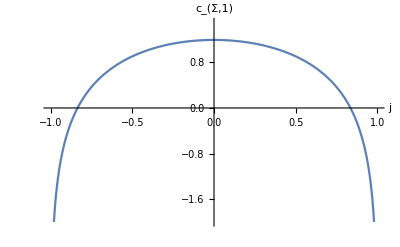

```mathematica
TT0=Plot[1/2+Log[2-2 jj]+Log[1+jj],{jj,-1,1},PlotRange->{-2,1.5},AxesLabel->{j,Text[Style[ToExpression["c_{\Sigma,1}",TeXForm,HoldForm],Small]]}]
```

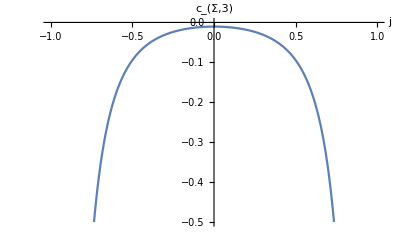

```mathematica
TT1=Plot[-(1+2 jj^2 (8+jj^2))/(96 (-1+jj^2)^2),{jj,-1,1},PlotRange->{-0.5,0},AxesLabel->{j,Text[Style[ToExpression["c_{\Sigma,3}",TeXForm,HoldForm],Small]]}]
```

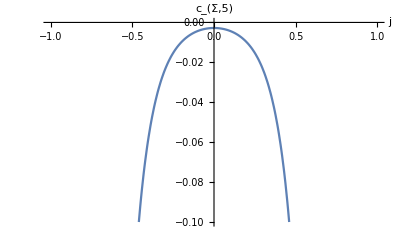

```mathematica
TT2=Plot[(-57+32 jj^2 (-86-106 jj^2-4 jj^4+jj^6))/(20480 (-1+jj^2)^4),{jj,-1,1},PlotRange->{-0.1,0},AxesLabel->{j,Text[Style[ToExpression["c_{\Sigma,5}",TeXForm,HoldForm],Small]]}]
```

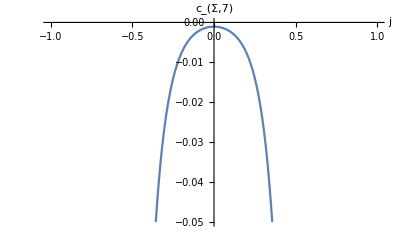

```mathematica
TT3=Plot[-(363+4 jj^2 (9273+37077 jj^2+16 jj^4 (1287+15 jj^2-6 jj^4+jj^6)))/(344064 (-1+jj^2)^6),{jj,-1,1},PlotRange->{-0.05,0},AxesLabel->{j,Text[Style[ToExpression["c_{\Sigma,7}",TeXForm,HoldForm],Small]]}]
```

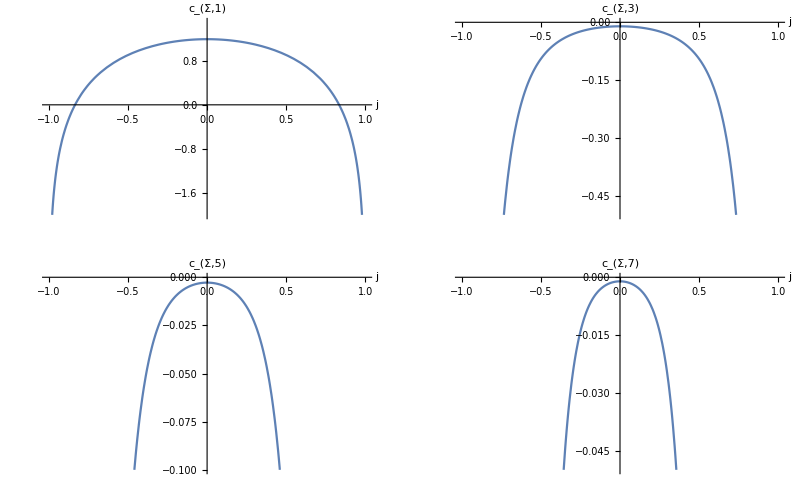

```mathematica
GraphicsGrid[{{TT0,TT1},{TT2,TT3}},Frame->All]
```

```mathematica
Coefficient[Actionnolog,e,0]/.{j->jj+2}
```

-1/2 (-1+jj) π

```mathematica
FullSimplify[Coefficient[Actionnolog,e,1],1<j<3&&h>0&&e>0]/.{j->jj+2}
```

-(h (1+Log[16]))/(2 √(-((-1+jj) (1+jj))))

```mathematica
Coefficient[Actionnolog,e,2]
```

0

```mathematica
(FullSimplify[Coefficient[Actionnolog,e,3],1<j<3&&h>0&&e>0]/.{j->jj+2})
```

-(h^3 (-74-(-2+jj) (2+jj) (22+(-2+jj) (2+jj)-24 Log[2])+102 Log[2]))/(48 (-((-1+jj) (1+jj)))^(7/2))

```mathematica
FullSimplify[Coefficient[Actionnolog,e,4],1<j<3&&h>0&&e>0]
```

0

```mathematica
FullSimplify[Coefficient[Actionnolog,e,5],1<j<3&&h>0&&e>0]/.{j->jj+2}
```

(h^5 (210267-269640 Log[2]-16 (-2+jj) (2+jj) ((-2+jj) (2+jj) (-771+2 (-2+jj) (2+jj) (2+(-2+jj) (2+jj))+840 Log[2])+1260 (-5+Log[64]))))/(20480 (-((-1+jj) (1+jj)))^(13/2))

```mathematica
FullSimplify[Coefficient[Actionnolog,e,7],1<j<3&&h>0&&e>0]/.{j->jj+2}
```

-1/(1376256 (-((-1+jj) (1+jj)))^(19/2))h^7 (3 (-46392011+56927640 Log[2])+4 (2+jj) (96455772-114550119 (2+jj)+75326760 (2+jj)^2-29800485 (2+jj)^3+7703616 (2+jj)^4-1934512 (2+jj)^5+798336 (2+jj)^6-328680 (2+jj)^7+91520 (2+jj)^8-15840 (2+jj)^9+1536 (2+jj)^10-64 (2+jj)^11+27720 (-2+jj) (1017+2 (-2+jj) (2+jj) (111+8 (-2+jj) (2+jj))) Log[2]))

```mathematica
Actionfaclogshift=Collect[FullSimplify[Normal[Action1factorlog+Action4faclog],e>0&&h>0&&1<j<3] ,e]/.{j->jj+2};
O1=FullSimplify[Coefficient[Actionfaclogshift,e,1] ,1<j<3&&e>0&&h!=0]/.{1-jj^2->aj}
O2=FullSimplify[Coefficient[Actionfaclogshift,e,2] ,1<j<3&&e>0&&h!=0]/.{1-jj^2->aj}
O3=FullSimplify[Coefficient[Actionfaclogshift,e,3] ,1<j<3&&e>0&&h>0]/.{1-jj^2->aj}
O4=FullSimplify[Coefficient[Actionfaclogshift,e,4] ,1<j<3&&e>0&&h!=0]/.{1-jj^2->aj}
O5=FullSimplify[Coefficient[Actionfaclogshift,e,5],1<j<3&&e>0&&h!=0]/.{1-jj^2->aj}
O6=FullSimplify[Coefficient[Actionfaclogshift,e,6],1<j<3&&e>0&&h!=0]/.{1-jj^2->aj}
O7=FullSimplify[Coefficient[Actionfaclogshift,e,7],1<j<3&&e>0&&h!=0]/.{1-jj^2->aj}
```

h/(2 √aj)

0

(h^3 (1+4 jj^2))/(32 aj^(7/2))

0

(21 h^5 (1+16 (jj^2+jj^4)))/(2048 aj^(13/2))

0

(165 h^7 (1+36 jj^2+120 jj^4+64 jj^6))/(32768 aj^(19/2))

```mathematica
J2sershift=-2*(Actionfaclogshift)
Normal[J2sershift]/.e->1;
Series[%,{h,0,ord}];
InverseSeries[%,h2];
BNF=FullSimplify[Series[Normal[%]/.{h2->h2*e},{e,0,ord}] ,1<j<3&&e>0&&h!=0]/.{1-jj^2->aj}
```

-2 (-(e h (-1+jj)^9 (1+jj)^9)/(2 (-((-1+jj) (1+jj)))^(19/2))+(e^3 h^3 (-1+jj)^6 (1+jj)^6 (17+4 (-2+jj) (2+jj)))/(32 (-((-1+jj) (1+jj)))^(19/2))-(21 e^5 h^5 (-1+jj)^3 (1+jj)^3 (321+16 (-2+jj) (2+jj) (9+(-2+jj) (2+jj))))/(2048 (-((-1+jj) (1+jj)))^(19/2))+(165 e^7 h^7 (6161+4 (-2+jj) (2+jj) (1017+2 (-2+jj) (2+jj) (111+8 (-2+jj) (2+jj)))))/(32768 (-((-1+jj) (1+jj)))^(19/2)))

-√aj h2 e+(h2^3 (1+4 jj^2) e^3)/(16 aj^(3/2))+(3 h2^5 (3+80 jj^2+48 jj^4) e^5)/(1024 aj^(7/2))+(3 h2^7 (15+1052 jj^2+2888 jj^4+960 jj^6) e^7)/(16384 aj^(11/2))+O[e]^8

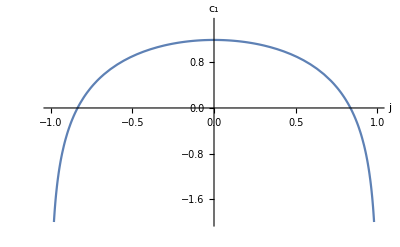

```mathematica
TTT0=Plot[1/2+Log[2-2 jj]+Log[1+jj],{jj,-1,1},PlotRange->{-2,1.5},AxesLabel->{j,Text[Style[ToExpression["c_{1}",TeXForm,HoldForm],Small]]}]
```

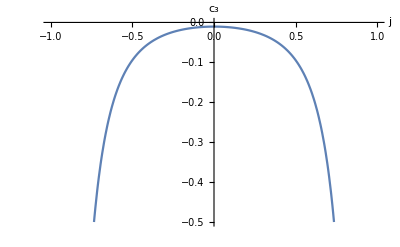

```mathematica
TTT1=Plot[-(1+2 jj^2 (8+jj^2))/(96 (-1+jj^2)^2),{jj,-1,1},PlotRange->{-0.5,0},AxesLabel->{j,Text[Style[ToExpression["c_{3}",TeXForm,HoldForm],Small]]}]
```

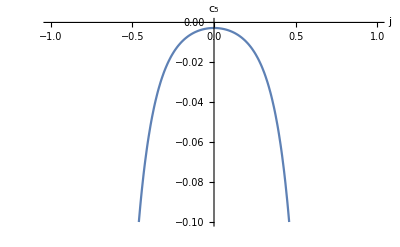

```mathematica
TTT2=Plot[(-57+32 jj^2 (-86-106 jj^2-4 jj^4+jj^6))/(20480 (-1+jj^2)^4),{jj,-1,1},PlotRange->{-0.1,0},AxesLabel->{j,Text[Style[ToExpression["c_{5}",TeXForm,HoldForm],Small]]}]
```

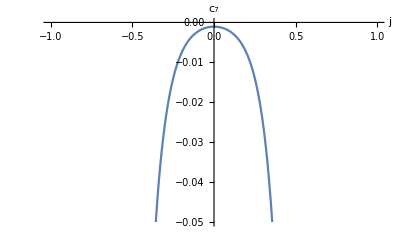

```mathematica
TTT3=Plot[-(363+4 jj^2 (9273+37077 jj^2+16 jj^4 (1287+15 jj^2-6 jj^4+jj^6)))/(344064 (-1+jj^2)^6),{jj,-1,1},PlotRange->{-0.05,0},AxesLabel->{j,Text[Style[ToExpression["c_{7}",TeXForm,HoldForm],Small]]}]
```

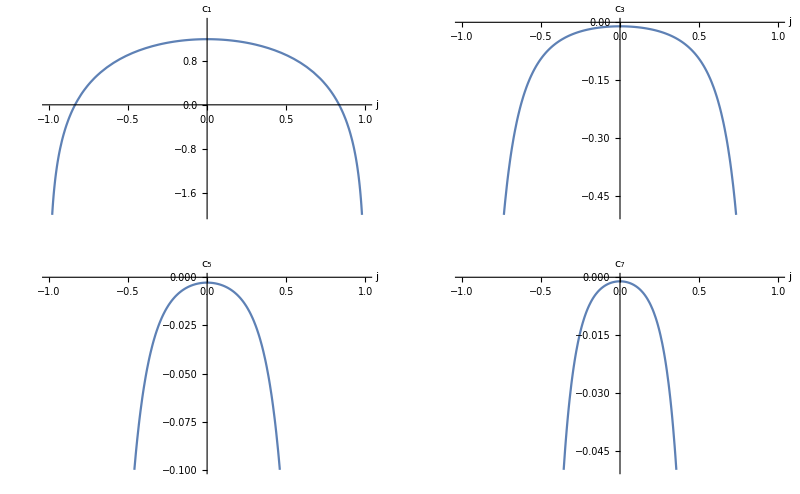

```mathematica
GraphicsGrid[{{TTT0,TTT1},{TTT2,TTT3}},Frame->All]
```